```mathematica
f[φ_]=-(9 φ^4-12 φ^3+30 φ^2-12 φ+1)/3;
g[φ_]=-2 (27 φ^6-54 φ^5-135 φ^4+180 φ^3-99 φ^2+18 φ-1)/27;
```

```mathematica
Δ[φ_]=-16(4 f[φ]^3+27 g[φ]^2);
```

```mathematica
Δ[φ]//FullSimplify
(*Ok! ChatGPT was right.*)
```

4096 (-1+φ)^3 φ^6 (-1+9 φ)

```mathematica
(*Define the moebius map that sends phi into an isogenous phi. Note: Moebius is not SL(2,ℤ)! But SL(2,ℤ) sits inside Moebius(ℂ).*)
mob[x_]=(x-1)/(9x-1);
```

```mathematica
Solve[mob[x]==x,x]
```

{{x→1/9 (1-2 ⅈ √2)},{x→1/9 (1+2 ⅈ √2)}}

```mathematica
mob[mob[x]]==x//FullSimplify
```

True

```mathematica
Δ[mob[x]]//FullSimplify
```

(16777216 (-1+x)^6 x^3)/(1-9 x)^10

```mathematica
Solve[Δ[mob[x]]==Δ[x],x]
```

{{x→0},{x→0},{x→0},{x→1},{x→1},{x→1},{x→1/9 (1-2 ⅈ √2)},{x→1/9 (1+2 ⅈ √2)},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→}}

```mathematica
a[φ_,α_]:=-α*φ^4+324*φ^3-810*φ^2+324*φ-27
b[φ_]:=-1458*φ^6+2916*φ^5+7290*φ^4-9720*φ^3+5346*φ^2-972*φ+54
Delta[phi_,α_]:=-16(4 a[phi,α]^3+27 b[phi]^2);
Delta[x,y]//FullSimplify
N[Delta[1,243]]
```

-16 (78732 (1-3 x (2+x))^2 (1+3 x (-4+x (10+3 (-4+x) x)))^2-4 (27-162 (-2+x) x (-1+2 x)+x^4 y)^3)

0.

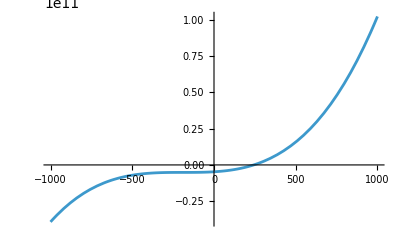

```mathematica
Plot[Delta[1,x],{x,-1000,1000}]
```

```mathematica
Delta[3,x]//FullSimplify
```

-16 (9755209728+4 (2403-81 x)^3)

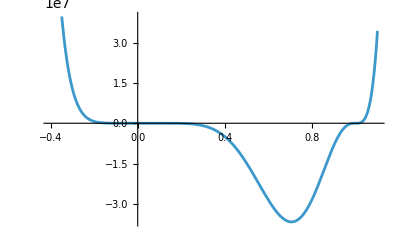

```mathematica
Plot[Delta[x,243],{x,-0.4,1.1}]
```

```mathematica
Delta[1/25,243]
```

481469424205824/95367431640625

```mathematica
p4[ϕ_]:=Sum[ToExpression["a"<>ToString[i]] ϕ^i,{i,0,4}];
p6[ϕ_]:=Sum[ToExpression["b"<>ToString[i]] ϕ^i,{i,0,6}];
Delta[ϕ_]=FullSimplify[4 p4[ϕ]^3+27 p6[ϕ]^2];
```

```mathematica
Solve[Delta[x]==0,x]
```

{{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,1]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,2]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,3]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,4]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,5]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,6]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,7]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,8]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,9]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,10]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,11]},{x→Root[4 a0^3+27 b0^2+(12 a0^2 a1+54 b0 b1) #1+(12 a0 a1^2+12 a0^2 a2+27 b1^2+54 b0 b2) #1^2+(4 a1^3+24 a0 a1 a2+12 a0^2 a3+54 b1 b2+54 b0 b3) #1^3+(12 a1^2 a2+12 a0 a2^2+24 a0 a1 a3+12 a0^2 a4+27 b2^2+54 b1 b3+54 b0 b4) #1^4+(12 a1 a2^2+12 a1^2 a3+24 a0 a2 a3+24 a0 a1 a4+54 b2 b3+54 b1 b4+54 b0 b5) #1^5+(4 a2^3+24 a1 a2 a3+12 a0 a3^2+12 a1^2 a4+24 a0 a2 a4+27 b3^2+54 b2 b4+54 b1 b5+54 b0 b6) #1^6+(12 a2^2 a3+12 a1 a3^2+24 a1 a2 a4+24 a0 a3 a4+54 b3 b4+54 b2 b5+54 b1 b6) #1^7+(12 a2 a3^2+12 a2^2 a4+24 a1 a3 a4+12 a0 a4^2+27 b4^2+54 b3 b5+54 b2 b6) #1^8+(4 a3^3+24 a2 a3 a4+12 a1 a4^2+54 b4 b5+54 b3 b6) #1^9+(12 a3^2 a4+12 a2 a4^2+27 b5^2+54 b4 b6) #1^10+(12 a3 a4^2+54 b5 b6) #1^11+(4 a4^3+27 b6^2) #1^12&,12]}}

```mathematica
Solve[x^2-11x-1==0,x]
```

{{x→1/2 (11-5 √5)},{x→1/2 (11+5 √5)}}

```mathematica
p6[x_]:=(x^2+1)(x^4-18 x^3+74 x^2+18x+1)
```

```mathematica
p6[x]//Expand
```

1+18 x+75 x^2+75 x^4-18 x^5+x^6

```mathematica
(*Finding the conifold points in moduli space for the HV manifold.*)
x=Table[ToExpression["x"<>ToString[i]],{i,1,5}];
p1[x_]:=Sum[x[[i]],{i,1,5}];
p2[x_]:=Sum[1/x[[i]],{i,1,5}];
p[x_,ϕ_]:=p1[x]p2[x]-1/ϕ;
eqns=Join[{p[x,ϕ]==0},Table[D[p[x,ϕ],x[[i]]]==0,{i,1,5}]];
vars=Join[x,{ϕ}];
sols=DeleteDuplicates[Solve[eqns,vars]];
Print["Double points found: ", Length[sols]];

ConifoldPhis=DeleteDuplicates[Table[sols[[i]][[-1]],{i,1,Length[sols]}]];
Print["Conifold points in moduli space: ",ConifoldPhis]

Hess[x_,ϕ_]:=Table[Table[D[D[(p[x,ϕ]),x[[i]]],x[[j]]],{j,{1,5}}],{i,{1,5}}];
Which[!MemberQ[Table[Det[Hess[x,ϕ]]/.sols[[i]],{i,1,Length[sols]}],0],
Print["All double points are conifold (nodal) singularities."],
True,
Print["There are double points which are not nodal singularities. More care is required."]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Double points found: 16

Conifold points in moduli space: {ϕ→1/9,ϕ→1,ϕ→1/25}

All double points are conifold (nodal) singularities.

```mathematica
(*It looks like the 1/25 point is associated to trivial representation of the permutation group on the nodal point coordinates.*)
sols
```

{{x1→-x3,x2→-x3,x4→-x3,x5→-x3,ϕ→1/9},{x1→-x3,x2→-x3,x4→x3,x5→-x3,ϕ→1},{x1→-x3,x2→-x3,x4→-x3,x5→x3,ϕ→1},{x1→-x3,x2→-x3,x4→x3,x5→x3,ϕ→1},{x1→-x3,x2→x3,x4→-x3,x5→-x3,ϕ→1},{x1→-x3,x2→x3,x4→x3,x5→-x3,ϕ→1},{x1→-x3,x2→x3,x4→-x3,x5→x3,ϕ→1},{x1→-x3,x2→x3,x4→x3,x5→x3,ϕ→1/9},{x1→x3,x2→-x3,x4→-x3,x5→-x3,ϕ→1},{x1→x3,x2→-x3,x4→x3,x5→-x3,ϕ→1},{x1→x3,x2→-x3,x4→-x3,x5→x3,ϕ→1},{x1→x3,x2→-x3,x4→x3,x5→x3,ϕ→1/9},{x1→x3,x2→x3,x4→-x3,x5→-x3,ϕ→1},{x1→x3,x2→x3,x4→x3,x5→-x3,ϕ→1/9},{x1→x3,x2→x3,x4→-x3,x5→x3,ϕ→1/9},{x1→x3,x2→x3,x4→x3,x5→x3,ϕ→1/25}}

```mathematica
(*Finding the conifold points in moduli space for the mirror bicubic.*)
x=Table[ToExpression["x"<>ToString[i]],{i,1,2}];
y=Table[ToExpression["y"<>ToString[i]],{i,1,2}];
p[x_,y_,ϕ_]:=x[[1]]x[[2]]y[[1]]y[[2]]+(x[[1]]^2 x[[2]]+x[[1]] x[[2]]^2-ϕ)y[[1]]y[[2]]+(y[[1]]^2 y[[2]]+y[[1]] y[[2]]^2-ϕ)x[[1]]x[[2]];
eqns=Join[{p[x,y,ϕ]==0},Table[D[p[x,y,ϕ],x[[i]]]==0,{i,1,2}],Table[D[p[x,y,ϕ],y[[i]]]==0,{i,1,2}]];
vars=Join[x,y,{ϕ}];
sols=FullSimplify[DeleteDuplicates[Solve[eqns,vars]]];
Print["Double points found: ", Length[sols]];

Hess[x_,y_,ϕ_]:=Join[Table[Join[Table[D[D[p[x,y,ϕ],x[[i]]],x[[j]]],{j,{1,2}}],Table[D[D[p[x,y,ϕ],x[[i]]],y[[j]]],{j,{1,2}}]],{i,{1,2}}],Table[Join[Table[D[D[p[x,y,ϕ],y[[i]]],x[[j]]],{j,{1,2}}],Table[D[D[p[x,y,ϕ],y[[i]]],y[[j]]],{j,{1,2}}]],{i,{1,2}}]];
Which[!MemberQ[Table[Det[Hess[x,y,ϕ]]/.sols[[i]],{i,1,Length[sols]}],0],
Print["All double points are conifold (nodal) singularities."],
True,
Print["There are double points which are not nodal singularities. More care is required."];
ConifoldIndexes=DeleteElements[Range[Length[sols]],Flatten[Position[Table[FullSimplify[Det[Hess[x,y,ϕ]]/.sols[[i]]],{i,1,Length[sols]}],0]]]];

ConifoldPhis=DeleteDuplicates[Table[sols[[i]][[-1]],{i,ConifoldIndexes}]];
Print["Conifold points in moduli space: ",ConifoldPhis]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Double points found: 33

There are double points which are not nodal singularities. More care is required.

Conifold points in moduli space: {y2→0,ϕ→1/216,ϕ→-1/27}

```mathematica
(*Once again, 1/216 (which is the conifold point that doesn't show up in the discriminant) is associated to the nodal point with all equal coordinates.*)
sols
```

{{x1→0,x2→0,ϕ→0},{x1→0,y1→0,ϕ→0},{x1→0,y2→0,ϕ→0},{x1→0,y2→-1-x2-y1,ϕ→0},{x2→0,y1→0,ϕ→0},{x2→0,y2→0,ϕ→0},{x2→0,y2→-1-x1-y1,ϕ→0},{x2→-1-x1-y2,y1→0,ϕ→0},{y1→0,y2→0,ϕ→0},{x2→-1-x1-y1,y2→0,ϕ→0},{x1→0,x2→0,y1→0,ϕ→0},{x1→0,x2→0,y2→0,ϕ→0},{x1→0,x2→0,y2→-1-y1,ϕ→0},{x1→-1/3-y1,x2→0,y2→0,ϕ→0},{x1→0,y1→-1/6,y2→0,ϕ→0},{x1→0,x2→0,y1→0,y2→0},{x2→-1-x1,y1→0,y2→0,ϕ→0},{x1→0,y1→0,y2→0,ϕ→0},{x2→0,y1→0,y2→0,ϕ→0},{x1→0,y1→-1/6 ⅈ (-ⅈ+√3),y2→0,ϕ→0},{x1→0,y1→1/6 ⅈ (ⅈ+√3),y2→0,ϕ→0},{x1→-1/6,x2→-1/6,y1→-1/6,y2→-1/6,ϕ→1/216},{x1→-1/6,x2→0,y1→-1/6,y2→0,ϕ→0},{x1→0,x2→0,y1→-1/6,y2→-5/6,ϕ→0},{x1→0,x2→0,y1→-1/6,y2→0,ϕ→0},{x1→0,x2→0,y1→-1/6 ⅈ (-ⅈ+√3),y2→0,ϕ→0},{x1→0,x2→0,y1→-1/6 ⅈ (-ⅈ+√3),y2→1/6 ⅈ (5 ⅈ+√3),ϕ→0},{x1→1/6 ⅈ (ⅈ+√3),x2→0,y1→-1/6 ⅈ (-ⅈ+√3),y2→0,ϕ→0},{x1→1/6 ⅈ (ⅈ+√3),x2→1/6 ⅈ (ⅈ+√3),y1→-1/6 ⅈ (-ⅈ+√3),y2→-1/6 ⅈ (-ⅈ+√3),ϕ→-1/27},{x1→0,x2→0,y1→1/6 ⅈ (ⅈ+√3),y2→0,ϕ→0},{x1→0,x2→0,y1→1/6 ⅈ (ⅈ+√3),y2→-1/6 ⅈ (-5 ⅈ+√3),ϕ→0},{x1→-1/6 ⅈ (-ⅈ+√3),x2→0,y1→1/6 ⅈ (ⅈ+√3),y2→0,ϕ→0},{x1→-1/6 ⅈ (-ⅈ+√3),x2→-1/6 ⅈ (-ⅈ+√3),y1→1/6 ⅈ (ⅈ+√3),y2→1/6 ⅈ (ⅈ+√3),ϕ→-1/27}}

```mathematica
U=Table[ToExpression["U"<>ToString[i]],{i,1,4}];
V=Table[ToExpression["V"<>ToString[i]],{i,1,4}];
vars=Join[U,V];
a=Table[1,{i,5}];
b=Join[{-ϕ},Table[1,{i,5}]];
c=Join[{-ϕ},Table[1,{i,5}]];
p[U_,V_,ϕ]:=Join[Table[a[[i]]+b[[i]]U[[i]]+c[[i]]V[[i]],{i,4}],{a[[5]]+b[[5]]/Product[U[[i]],{i,4}]+c[[5]]/Product[V[[i]],{i,4}]}];
eqns=Join[Table[p[U,V,ϕ][[i]]==0,{i,5}],Flatten[Table[Table[D[p[U,V,ϕ][[j]],vars[[i]]]==0,{j,5}],{i,1,Length[vars]}]]];
sols=FullSimplify[DeleteDuplicates[Solve[eqns,Append[vars,ϕ]]]];
Print["Double points found: ", Length[sols]];
```

Double points found: 0

```mathematica
p[U,V,ϕ]
```

{1-U1 ϕ-V1 ϕ,1+U2+V2,1+U3+V3,1+U4+V4,1+1/(U1 U2 U3 U4)+1/(V1 V2 V3 V4)}

```mathematica
eqns
```

{1-U1 ϕ-V1 ϕ==0,1+U2+V2==0,1+U3+V3==0,1+U4+V4==0,1+1/(U1 U2 U3 U4)+1/(V1 V2 V3 V4)==0,-ϕ==0,True,True,True,-1/(U1^2 U2 U3 U4)==0,True,False,True,True,-1/(U1 U2^2 U3 U4)==0,True,True,False,True,-1/(U1 U2 U3^2 U4)==0,True,True,True,False,-1/(U1 U2 U3 U4^2)==0,-ϕ==0,True,True,True,-1/(V1^2 V2 V3 V4)==0,True,False,True,True,-1/(V1 V2^2 V3 V4)==0,True,True,False,True,-1/(V1 V2 V3^2 V4)==0,True,True,True,False,-1/(V1 V2 V3 V4^2)==0}

```mathematica
(*Finding the conifold points in moduli space for the mirror split quintic.*)
U=Table[ToExpression["U"<>ToString[i]],{i,1,4}];
V=Table[ToExpression["V"<>ToString[i]],{i,1,4}];
vars=Join[U,V];
a=Table[1,{i,5}];
b=Join[{-ϕ},Table[1,{i,5}]];
c=Join[{-ϕ},Table[1,{i,5}]];
p[U_,V_,ϕ]:=Join[Table[a[[i]]+b[[i]]U[[i]]+c[[i]]V[[i]],{i,4}],{a[[5]]+b[[5]]/Product[U[[i]],{i,4}]+c[[5]]/Product[V[[i]],{i,4}]}];
eqns=Join[Table[p[U,V,ϕ][[i]]==0,{i,5}],Flatten[Table[Table[D[p[U,V,ϕ][[j]],vars[[i]]]==0,{j,5}],{i,1,Length[vars]}]]];
sols=FullSimplify[DeleteDuplicates[Solve[eqns,Append[vars,ϕ]]]];
Print["Double points found: ", Length[sols]];
```

Double points found: 0

```mathematica
(*This is consistent with the fact that the discriminant of the elliptic curve doesn't have any rational root other than 0, which is presumably the LCS even in this case.*)
```